```mathematica
rapp[x1_,x2_]:=Table[{x1[[i,1]],x1[[i,2]]/x2[[i,2]]},{i,1,Length[x1]}]
absrapp[x1_,x2_]:=Table[{x1[[i,1]],Abs[x1[[i,2]]/x2[[i,2]]]},{i,1,Length[x1]}]
mult[x1_,x2_]:=Table[{x1[[i,1]],x1[[i,2]]*x2[[i,2]]},{i,1,Length[x1]}]
sum[x1_,x2_]:=Table[{x1[[i,1]],x1[[i,2]]+x2[[i,2]]},{i,1,Length[x1]}]
sumlist[x1_]:=Table[{x1[[1,i,1]],x1[[1,i,2]]+x1[[2,i,2]]+x1[[3,i,2]]},{i,1,Length[x1[[1]]]}]
coeff[x1_,c_]:=Table[{x1[[i,1]],x1[[i,2]]*c},{i,1,Length[x1]}]
sumconst[x1_,c_]:=Table[{x1[[i,1]],x1[[i,2]]+c},{i,1,Length[x1]}]
diff[x1_,x2_]:=Table[{x1[[i,1]],x1[[i,2]]-x2[[i,2]]},{i,1,Length[x1]}]
joinbin[x_,n_]:=Map[{(Plus@@#)[[1]]/n,(Plus@@#)[[2]]}&,Partition[x,n]]
```

```mathematica
Estrai[filename_,histo_,namehisto_,nhisto_]:=Module[{file,positions,binning},
histo=.;
namehisto=.;
nhisto=.;
file=Import[filename,"Table"];
nhisto=0;
namehisto=Table[0,{j,1,100}];
positions=Table[0,{j,1,100}];
Do[
If[file[[i]]=={"<Histo>"}, 
nhisto=nhisto+1;
namehisto[[nhisto]]=file[[i+2]];
positions[[nhisto]]=i];
     ,{i,1,Length[file]}];
namehisto=Take[namehisto,nhisto];
positions=Take[positions,nhisto];
Do[(*Print[file[[ positions[[i]]+4 ]] ];*)binning[i]=file[[ positions[[i]]+4 ]];passo[i]=(binning[i][[3]]-binning[i][[2]])/binning[i][[1]],{i,1,nhisto}];
 Do[histo[i]=Table[{binning[i][[2]]+(j-1)passo[i],file[[positions[[i]]+18+j ,1 ]]},{j,0,binning[i][[1]]+1}],{i,1,nhisto}]
]
```

```mathematica
namerun="tretevnocuts";
```

```mathematica
namefolder="2to4_mumuttbar_onlyWeak";
NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/DavideMG5Runs/"<>namefolder<>"/HTML/"<>namerun<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MmumuOW =prova[12];
MttOW =prova[16];


namefolder="2to4_mumuttbar_onlyQED";
NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/DavideMG5Runs/"<>namefolder<>"/HTML/"<>namerun<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MmumuOQ =prova[12];
MttOQ =prova[16];

(*NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/DavideMG5Runs/"<>namefolder<>"/HTML/"<>namerun<>"mllminduecentoOK"<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"mllminduecentoOK"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MmumuOQmllmin200 =prova[12];
MttOQmllmin200 =prova[16];*)
```

```mathematica
namefolder="2to4_mumuttbar";
NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/DavideMG5Runs/"<>namefolder<>"/HTML/"<>namerun<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MmumuWandQ =prova[12];
MttWandQ =prova[16];



namefolder="ZZ_to_tt_massivemu";
NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/DavideMG5Runs/"<>namefolder<>"/HTML/"<>namerun<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MttOWfromEVA =prova[8];


namefolder="VVneutral_to_tt_massivemu";
NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/DavideMG5Runs/"<>namefolder<>"/HTML/"<>namerun<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MttfromEVA =prova[8];
```

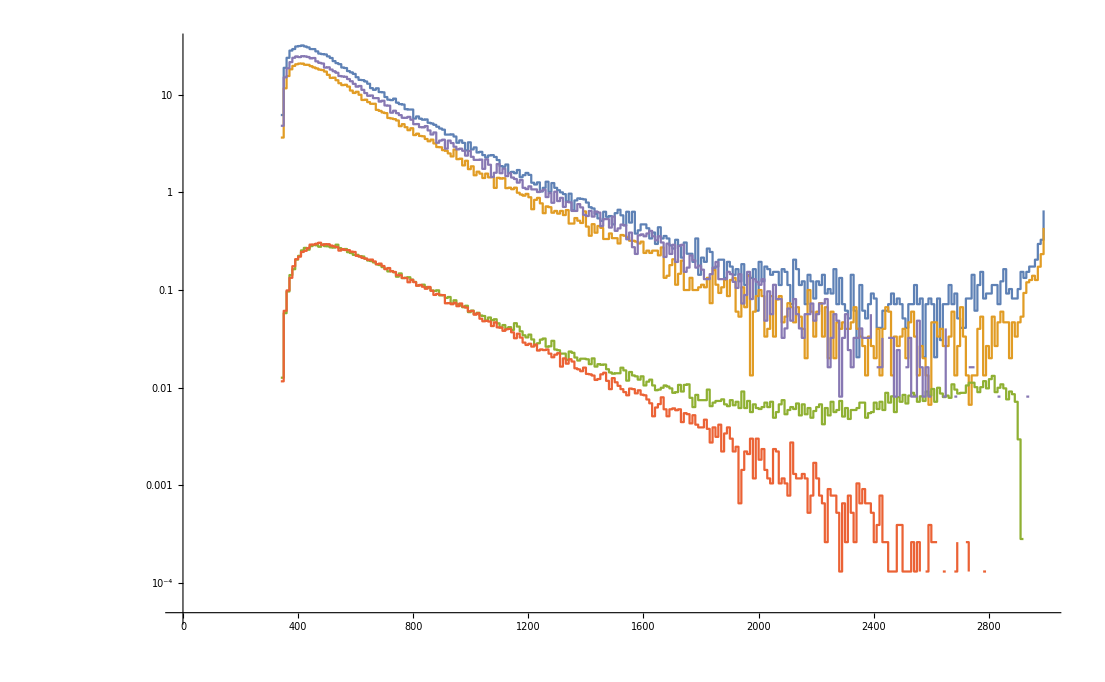

```mathematica
ListLogPlot[{MttWandQ,MttOQ,MttOW,MttOWfromEVA,MttfromEVA},Joined->True,InterpolationOrder->0]
```

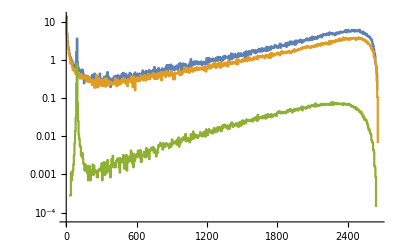

```mathematica
ListLogPlot[{MmumuWandQ,MmumuOQ,MmumuOW},Joined->True,InterpolationOrder->0]
```

```mathematica
namesruns={"unotevnocuts","tretevnocuts","diecitevnocuts"(*,"unotevmllmaxduecento","tretevmllmaxduecento","diecitevmllmaxduecento"*)}
```

{unotevnocuts,tretevnocuts,diecitevnocuts}

```mathematica
{"unotevnocuts","tretevnocuts","diecitevnocuts","unotevmllmaxduecento","tretevmllmaxduecento","diecitevmllmaxduecento"}
```

{unotevnocuts,tretevnocuts,diecitevnocuts,unotevmllmaxduecento,tretevmllmaxduecento,diecitevmllmaxduecento}

```mathematica
Do[

nbintogether=1;



namerun=namesruns[[i]];

subdir="nocuts";


Which[StringMatchQ[namesruns[[i]],"*maxduecento*"],subdir="mllmaxduecento"
];


Which[StringMatchQ[namesruns[[i]],"*uno*"],nbintogether=2,
StringMatchQ[namesruns[[i]],"*tre*"],nbintogether=10,
StringMatchQ[namesruns[[i]],"*dieci*"],nbintogether=20(*,
StringMatchQ[namesruns[[i]],"*cento*"],nbintogether=40*)];

Which[StringMatchQ[namesruns[[i]],"*uno*"],maxrange=5;maxrangeX=1000,
StringMatchQ[namesruns[[i]],"*tre*"],maxrange=65;maxrangeX=3000,
StringMatchQ[namesruns[[i]],"*dieci*"],maxrange=220;maxrangeX=10000(*,
StringMatchQ[namesruns[[i]],"*cento*"],nbintogether=40*)];

maxrangeXmll=maxrangeX;

Which[StringMatchQ[namesruns[[i]],"*maxduecento*"],maxrangeXmll=200
];


namefolder="2to4_mumuttbar_onlyWeak";
NameH=.;
NH=.;
Estrai["/Users/pagani/mu-vbf/DavideMG5Runs/"<>namefolder<>"/HTML/"<>namerun<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH];
MmumuOW =joinbin[prova[12],nbintogether];
MttOW =joinbin[prova[16],nbintogether];
etamupOW =joinbin[prova[9],1];


If[!StringMatchQ[namesruns[[i]],"*maxduecento*"],NameH=.;
NH=.;
Estrai["/Users/pagani/mu-vbf/DavideMG5Runs/"<>namefolder<>"/HTML/"<>StringDrop[namerun,-6]<>"mllminduecentoOK"<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>StringDrop[namerun,-6]<>"mllminduecentoOK"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH];
MmumuOWmllmin200 =joinbin[prova[12],nbintogether];
MttOWmllmin200 =joinbin[prova[16],nbintogether];
etamupOWmllmin200=joinbin[prova[9],1];



NameH=.;
NH=.;
Estrai["/Users/pagani/mu-vbf/DavideMG5Runs/"<>namefolder<>"/HTML/"<>namerun<>"emitwohalf"<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"emitwohalf"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH];
MmumuOWemi2p5 =joinbin[prova[12],nbintogether];
MttOWemi2p5 =joinbin[prova[16],nbintogether];
etamupOWemi2p5=joinbin[prova[9],1];

If[namerun==="tretevnocuts",MmumuOWemi2p5 =coeff[MmumuOWemi2p5 ,100000/45694];MttOWemi2p5 =coeff[MttOWemi2p5 ,100000/45694];etamupOWemi2p5 =coeff[etamupOWemi2p5 ,100000/45694]];


NameH=.;
NH=.;
Estrai["/Users/pagani/mu-vbf/DavideMG5Runs/"<>namefolder<>"/HTML/"<>namerun<>"emifive"<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"emifive"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH];
MmumuOWemi5 =joinbin[prova[12],nbintogether];
MttOWemi5 =joinbin[prova[16],nbintogether];
etamupOWemi5=joinbin[prova[9],1];





];








namefolder="2to4_mumuttbar_onlyQED";
NameH=.;
NH=.;
Estrai["/Users/pagani/mu-vbf/DavideMG5Runs/"<>namefolder<>"/HTML/"<>namerun<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH];
MmumuOQ =joinbin[prova[12],nbintogether];
MttOQ =joinbin[prova[16],nbintogether];
etamupOQ =joinbin[prova[9],1];

If[!StringMatchQ[namesruns[[i]],"*maxduecento*"],
NameH=.;
NH=.;
Estrai["/Users/pagani/mu-vbf/DavideMG5Runs/"<>namefolder<>"/HTML/"<>StringDrop[namerun,-6]<>"mllminduecentoOK"<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>StringDrop[namerun,-6]<>"mllminduecentoOK"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH];
MmumuOQmllmin200 =joinbin[prova[12],nbintogether];
MttOQmllmin200 =joinbin[prova[16],nbintogether];
etamupOQmllmin200=joinbin[prova[9],1];


NameH=.;
NH=.;
Estrai["/Users/pagani/mu-vbf/DavideMG5Runs/"<>namefolder<>"/HTML/"<>namerun<>"emitwohalf"<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"emitwohalf"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH];
MmumuOQemi2p5 =joinbin[prova[12],nbintogether];
MttOQemi2p5 =joinbin[prova[16],nbintogether];
etamupOQemi2p5=joinbin[prova[9],1];


NameH=.;
NH=.;
Estrai["/Users/pagani/mu-vbf/DavideMG5Runs/"<>namefolder<>"/HTML/"<>namerun<>"emifive"<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"emifive"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH];
MmumuOQemi5 =joinbin[prova[12],nbintogether];
MttOQemi5 =joinbin[prova[16],nbintogether];
etamupOQemi5=joinbin[prova[9],1];



];















namefolder="2to4_mumuttbar";
NameH=.;
NH=.;
Estrai["/Users/pagani/mu-vbf/DavideMG5Runs/"<>namefolder<>"/HTML/"<>namerun<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH];
MmumuWandQ =joinbin[prova[12],nbintogether];
MttWandQ =joinbin[prova[16],nbintogether];
etamupWandQ=joinbin[prova[9],1];
If[namerun==="unotevnocuts",MmumuWandQ=coeff[MmumuWandQ,100000/16125];MttWandQ=coeff[MttWandQ,100000/16125];etamupWandQ=coeff[etamupWandQ,100000/16125]];

If[!StringMatchQ[namesruns[[i]],"*maxduecento*"],NameH=.;
NH=.;
Estrai["/Users/pagani/mu-vbf/DavideMG5Runs/"<>namefolder<>"/HTML/"<>StringDrop[namerun,-6]<>"mllminduecentoOK"<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>StringDrop[namerun,-6]<>"mllminduecentoOK"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH];
MmumuWandQmllmin200 =joinbin[prova[12],nbintogether];
MttWandQmllmin200 =joinbin[prova[16],nbintogether];
etamupWandQmllmin200 =joinbin[prova[9],1];


NameH=.;
NH=.;
Estrai["/Users/pagani/mu-vbf/DavideMG5Runs/"<>namefolder<>"/HTML/"<>namerun<>"emitwohalf"<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"emitwohalf"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH];
MmumuWandQemi2p5 =joinbin[prova[12],nbintogether];
MttWandQemi2p5 =joinbin[prova[16],nbintogether];
etamupWandQemi2p5=joinbin[prova[9],1];
If[namerun==="unotevnocuts",MmumuWandQemi2p5 =coeff[MmumuWandQemi2p5 ,100000/16572];MttWandQemi2p5 =coeff[MttWandQemi2p5 ,100000/16572];etamupWandQemi2p5 =coeff[etamupWandQemi2p5 ,100000/16572]];


;

NameH=.;
NH=.;
Estrai["/Users/pagani/mu-vbf/DavideMG5Runs/"<>namefolder<>"/HTML/"<>namerun<>"emifive"<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"emifive"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH];
MmumuWandQemi5 =joinbin[prova[12],nbintogether];
MttWandQemi5 =joinbin[prova[16],nbintogether];
etamupWandQemi5=joinbin[prova[9],1];
If[namerun==="unotevnocuts",MmumuWandQemi5 =coeff[MmumuWandQemi5 ,100000/8272];MttWandQemi5 =coeff[MttWandQemi5 ,100000/8272];etamupWandQemi5 =coeff[etamupWandQemi5 ,100000/8272]];




];











If[!StringMatchQ[namesruns[[i]],"*maxduecento*"],

namefolder="ZZ_to_tt_massivemu";
NameH=.;
NH=.;
Estrai["/Users/pagani/mu-vbf/DavideMG5Runs/"<>namefolder<>"/HTML/"<>namerun<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH];
MttOWfromEVA =joinbin[prova[9],1];


namefolder="VVneutral_to_tt_massivemu";
NameH=.;
NH=.;
Estrai["/Users/pagani/mu-vbf/DavideMG5Runs/"<>namefolder<>"/HTML/"<>namerun<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH];
MttfromEVA =joinbin[prova[9],1];

];



namefolder="2to4_mupemttbar_onlyWeak";
NameH=.;
NH=.;
Estrai["/Users/pagani/mu-vbf/DavideMG5Runs/"<>namefolder<>"/HTML/"<>namerun<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH];
MttOWmue =joinbin[prova[21],nbintogether];
etamupOWmue=joinbin[prova[7],1];







namefolder="2to4_mupemttbar";
NameH=.;
NH=.;
Estrai["/Users/pagani/mu-vbf/DavideMG5Runs/"<>namefolder<>"/HTML/"<>namerun<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH];
MttWandQmue =joinbin[prova[21],nbintogether];
etamupWandQmue=joinbin[prova[7],1];
If[namerun==="diecitevnocuts",MttWandQmue=coeff[MttWandQmue,100000/10909];etamupWandQmue=coeff[etamupWandQmue,100000/10909]];






If[!StringMatchQ[namesruns[[i]],"*maxduecento*"],
NameH=.;
NH=.;
Estrai["/Users/pagani/mu-vbf/DavideMG5Runs/"<>namefolder<>"/HTML/"<>StringDrop[namerun,-6]<>"mllminduecentoOKOK"<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>StringDrop[namerun,-6]<>"mllminduecentoOK"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH];
MttWandQmuemllmin200 =joinbin[prova[21],nbintogether];
etamupWandQmuemllmin200=joinbin[prova[7],1];

NameH=.;
NH=.;
Estrai["/Users/pagani/mu-vbf/DavideMG5Runs/"<>namefolder<>"/HTML/"<>namerun<>"emitwohalf"<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"emitwohalf"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH];
MttWandQmueemi2p5 =joinbin[prova[21],nbintogether];
etamupWandQmueemi2p5=joinbin[prova[7],1];

NameH=.;
NH=.;
Estrai["/Users/pagani/mu-vbf/DavideMG5Runs/"<>namefolder<>"/HTML/"<>namerun<>"emifive"<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"emifive"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH];
MttWandQmueemi5 =joinbin[prova[21],nbintogether];
etamupWandQmueemi5=joinbin[prova[7],1];




];











Mmumuplot=ListLogPlot[{MmumuWandQ,MmumuOQ,MmumuOW,MmumuOQmllmin200,MmumuOQemi2p5, MmumuOQemi5},Joined->True,InterpolationOrder->0,PlotLabel->"ttbar",PlotLegends->{"mumu->ttmumu","mumu->ttmumu Only QED","mumu->ttmumu No QED","mumu->ttmumu No QED (mll>200)","mumu->ttmumu Only QED emi 2.5","mumu->ttmumu Only QED emi 5"},AxesLabel->{"m(mumu) [GeV]","σ[pb]"},PlotRange->{{0,maxrangeXmll},{0,maxrange}}];
Mmumuplotlinear=ListPlot[{MmumuWandQ,MmumuOQ,MmumuOW,MmumuOQmllmin200,MmumuOQemi2p5, MmumuOQemi5},Joined->True,InterpolationOrder->0,PlotLabel->"ttbar(Linear)",PlotLegends->{"mumu->ttmumu","mumu->ttmumu Only QED","mumu->ttmumu No QED","mumu->ttmumu No QED (mll>200)","mumu->ttmumu Only QED emi 2.5","mumu->ttmumu Only QED emi 5"},AxesLabel->{"m(mumu) [GeV]","σ[pb]"},PlotRange->{{0,maxrangeXmll},{0,maxrange}}];


If[!StringMatchQ[namesruns[[i]],"*maxduecento*"],

Mttplot=ListLogPlot[{MttWandQ,MttOQ,MttOW,MttOWfromEVA,MttfromEVA ,MttOWmue},Joined->True,InterpolationOrder->0,PlotLabel->"ttbar",PlotLegends->{"mumu->ttmumu","mumu->ttmumu Only QED","mumu->ttmumu No QED", "ZZ->tt EVA", "V=Z,a VV->tt EVA","mue->ttmue No QED"},AxesLabel->{"m(tt) [GeV]","σ[pb]"}];
Mttplotlinear=ListPlot[{MttWandQ,MttOQ,MttOW,MttOWfromEVA,MttfromEVA,MttOWmue },Joined->True,InterpolationOrder->0,PlotLabel->"ttbar (Linear)",PlotLegends->{"mumu->ttmumu","mumu->ttmumu Only QED","mumu->ttmumu No QED", "ZZ->tt EVA", "V=Z,a VV->tt EVA","mue->ttmue No QED"},AxesLabel->{"m(tt) [GeV]","σ[pb]"},PlotRange->{{0,maxrangeX},{0,maxrange*5}}];
Mttratio=ListPlot[{rapp[MttOW,MttOWfromEVA],rapp[MttOWmue,MttOWfromEVA] },Joined->True,InterpolationOrder->0,PlotLabel->"ttbar ratio over ZZ->tt EVA",PlotLegends->{"mumu->ttmumu No QED","mue->ttmue No QED"},AxesLabel->{"m(tt) [GeV]","ratio"},PlotRange->{{0,maxrangeX},{0,2}}];


Mttplotmllgt200=ListLogPlot[{MttWandQmllmin200,MttOQmllmin200,MttOWmllmin200,MttOWfromEVA,MttfromEVA,MttOWmue },Joined->True,InterpolationOrder->0,PlotLabel->"ttbar (mll > 200)",PlotLegends->{"mumu->ttmumu","mumu->ttmumu Only QED","mumu->ttmumu No QED", "ZZ->tt EVA", "V=Z,a VV->tt EVA","mue->ttmue No QED (no mllcut)"},AxesLabel->{"m(tt) [GeV]","σ[pb]"}];
Mttplotlinearmllgt200=ListPlot[{MttWandQmllmin200,MttOQmllmin200,MttOWmllmin200,MttOWfromEVA,MttfromEVA,MttOWmue },Joined->True,InterpolationOrder->0,PlotLabel->"ttbar (mll > 200) (Linear)",PlotLegends->{"mumu->ttmumu","mumu->ttmumu Only QED","mumu->ttmumu No QED", "ZZ->tt EVA", "V=Z,a VV->tt EVA","mue->ttmue No QED (no mllcut)"},AxesLabel->{"m(tt) [GeV]","σ[pb]"},PlotRange->{{0,maxrangeX},{0,maxrange*5}}];
Mttratiomllgt200=ListPlot[{rapp[MttOWmllmin200,MttOWfromEVA],rapp[MttOWmue,MttOWfromEVA] },Joined->True,InterpolationOrder->0,PlotLabel->"ttbar ratio over ZZ->tt EVA (mll > 200)",PlotLegends->{"mumu->ttmumu No QED","mue->ttmue No QED (no mllcut)"},AxesLabel->{"m(tt) [GeV]","σ[pb]"},PlotRange->{{0,maxrangeX},{0,2}}];


Mttplotmllcutsornot=ListLogPlot[{MttWandQ,MttOQ,MttOW,MttWandQmllmin200,MttOQmllmin200,MttOWmllmin200 ,MttOWmue},Joined->True,InterpolationOrder->0,PlotLabel->"ttbar(nocut and mll > 200)",PlotLegends->{"mumu->ttmumu","mumu->ttmumu Only QED","mumu->ttmumu No QED","mumu->ttmumu mll>200","mumu->ttmumu Only QED mll>200","mumu->ttmumu No QED mll>200","mue->ttmue No QED (no mllcut)"},AxesLabel->{"m(tt) [GeV]","σ[pb]"}];

Mttplotlinearmllcutsornot=ListPlot[{MttWandQ,MttOQ,MttOW,MttWandQmllmin200,MttOQmllmin200,MttOWmllmin200,MttOWmue },Joined->True,InterpolationOrder->0,PlotLabel->"ttbar(nocut and mll > 200) (Linear)",PlotLegends->{"mumu->ttmumu","mumu->ttmumu Only QED","mumu->ttmumu No QED","mumu->ttmumu mll>200","mumu->ttmumu Only QED mll>200","mumu->ttmumu No QED mll>200","mue->ttmue No QED (no mllcut)"},AxesLabel->{"m(tt) [GeV]","σ[pb]"},PlotRange->{{0,maxrangeX},{0,maxrange*5}}];






MttplotcutsornotOQ=ListLogPlot[{MttOQ,MttOQmllmin200,MttOQemi2p5,MttOQemi5},Joined->True,InterpolationOrder->0,PlotLabel->"ttbar(nocut, mll and emi cuts)",PlotLegends->{"mumu->ttmumu Only QED","mumu->ttmumu Only QED mll>200","mumu->ttmumu Only QED emicut 2.5","mumu->ttmumu Only QED emicut 5"},AxesLabel->{"m(tt) [GeV]","σ[pb]"}];

MttplotcutsornotOW=ListLogPlot[{MttOW,MttOWmllmin200,MttOWemi2p5,MttOWemi5},Joined->True,InterpolationOrder->0,PlotLabel->"ttbar(nocut, mll and emi cuts)",PlotLegends->{"mumu->ttmumu NO QED","mumu->ttmumu NO QED mll>200","mumu->ttmumu NO QED emicut 2.5","mumu->ttmumu NO QED emicut 5"},AxesLabel->{"m(tt) [GeV]","σ[pb]"}];


Mttplotcutsornot=ListLogPlot[{MttWandQ,MttWandQmllmin200,MttWandQemi2p5,MttWandQemi5},Joined->True,InterpolationOrder->0,PlotLabel->"ttbar(nocut, mll and emi cuts)",PlotLegends->{"mumu->ttmumu","mumu->ttmumu mll>200","mumu->ttmumu emicut 2.5","mumu->ttmumu emicut 5"},AxesLabel->{"m(tt) [GeV]","σ[pb]"}];





Mttplotcutsornotmue=ListLogPlot[{MttWandQmue,MttWandQmuemllmin200,MttWandQmueemi2p5,MttWandQmueemi5},Joined->True,InterpolationOrder->0,PlotLabel->"ttbar(nocut, mll and emi cuts)",PlotLegends->{"mupe->ttmupe","mupe->ttmupe mll>200","mupe->ttmupe emicut 2.5","mupe->ttmupe emicut 5"},AxesLabel->{"m(tt) [GeV]","σ[pb]"}];




MarcoMttplotcutsornot=ListLogPlot[{MttWandQ,MttWandQmllmin200,MttWandQmueemi2p5,MttWandQmueemi5},Joined->True,InterpolationOrder->0,PlotLabel->"ttbar(nocut, mll and emi cuts)",PlotLegends->{"mumu->ttmumu (NO CUTS, not in Marco plot)","mumu->ttmumu mll>200","mupe->ttmupe emicut 2.5","mupe->ttmupe emicut 5"},AxesLabel->{"m(tt) [GeV]","σ[pb]"}];





MarcoMttplotcutsornotlinear=ListPlot[{MttWandQ,MttWandQmllmin200,MttWandQmueemi2p5,MttWandQmueemi5},Joined->True,InterpolationOrder->0,PlotLabel->"ttbar(nocut, mll and emi cuts)",PlotLegends->{"mumu->ttmumu (NO CUTS, not in Marco plot)","mumu->ttmumu mll>200","mupe->ttmupe emicut 2.5","mupe->ttmupe emicut 5"},AxesLabel->{"m(tt) [GeV]","σ[pb]"},PlotRange->{{0,maxrangeX},{0,maxrange*5}}];


MarcoMttplotcutsornotratio=ListPlot[{rapp[MttWandQ,MttWandQmllmin200],rapp[MttWandQmllmin200,MttWandQmllmin200],rapp[MttWandQmueemi2p5,MttWandQmllmin200],rapp[MttWandQmueemi5,MttWandQmllmin200]},Joined->True,InterpolationOrder->0,PlotLabel->"ttbar(nocut, mll and emi cuts) ratio over mumu->ttmumu mll>200 ",PlotLegends->{"mumu->ttmumu (NO CUTS, not in Marco plot)","mumu->ttmumu mll>200","mupe->ttmupe emicut 2.5","mupe->ttmupe emicut 5"},AxesLabel->{"m(tt) [GeV]","σ[pb]"}];




Mttratiocutsnocut=ListPlot[{rapp[MttWandQmllmin200,MttWandQ],rapp[MttOQmllmin200,MttOQ],rapp[MttOWmllmin200,MttOW] },Joined->True,InterpolationOrder->0,PlotLabel->"ttbar ratio (mll > 200)/(no cuts)",PlotLegends->{"mumu->ttmumu","mumu->ttmumu Only QED","mumu->ttmumu No QED"},AxesLabel->{"m(tt) [GeV]","σ[pb]"},PlotRange->{{0,maxrangeX},{0,2}},PlotRange->{{0,maxrangeX},{0.8,1.5}}];


Mttratiocutsnocutemi5=ListPlot[{rapp[MttWandQemi5,MttWandQ],rapp[MttOQemi5,MttOQ],rapp[MttOWemi5,MttOW] },Joined->True,InterpolationOrder->0,PlotLabel->"ttbar ratio (emiy=5)/(no cuts)",PlotLegends->{"mumu->ttmumu","mumu->ttmumu Only QED","mumu->ttmumu No QED"},AxesLabel->{"m(tt) [GeV]","σ[pb]"},PlotRange->{{0,maxrangeX},{0,2}},PlotRange->{{0,maxrangeX},{0.8,1.5}}];





(**eta**)


etamupplotmllcutsornot=ListLogPlot[{etamupWandQ,etamupOQ,etamupOW,etamupWandQmllmin200,etamupOQmllmin200,etamupOWmllmin200 ,etamupOWmue},Joined->True,InterpolationOrder->0,PlotLabel->"ttbar(nocut and mll > 200)",PlotLegends->{"mumu->ttmumu","mumu->ttmumu Only QED","mumu->ttmumu No QED","mumu->ttmumu mll>200","mumu->ttmumu Only QED mll>200","mumu->ttmumu No QED mll>200","mue->ttmue No QED (no mllcut)"},AxesLabel->{"eta mu+","σ[pb]"}];

etamupplotlinearmllcutsornot=ListPlot[{etamupWandQ,etamupOQ,etamupOW,etamupWandQmllmin200,etamupOQmllmin200,etamupOWmllmin200,etamupOWmue },Joined->True,InterpolationOrder->0,PlotLabel->"ttbar(nocut and mll > 200) (Linear)",PlotLegends->{"mumu->ttmumu","mumu->ttmumu Only QED","mumu->ttmumu No QED","mumu->ttmumu mll>200","mumu->ttmumu Only QED mll>200","mumu->ttmumu No QED mll>200","mue->ttmue No QED (no mllcut)"},AxesLabel->{"eta mu+","σ[pb]"}];






etamupplotcutsornotOQ=ListLogPlot[{etamupOQ,etamupOQmllmin200,etamupOQemi2p5,etamupOQemi5},Joined->True,InterpolationOrder->0,PlotLabel->"ttbar(nocut, mll and emi cuts)",PlotLegends->{"mumu->ttmumu Only QED","mumu->ttmumu Only QED mll>200","mumu->ttmumu Only QED emicut 2.5","mumu->ttmumu Only QED emicut 5"},AxesLabel->{"eta mu+","σ[pb]"}];

etamupplotcutsornotOW=ListLogPlot[{etamupOW,etamupOWmllmin200,etamupOWemi2p5,etamupOWemi5},Joined->True,InterpolationOrder->0,PlotLabel->"ttbar(nocut, mll and emi cuts)",PlotLegends->{"mumu->ttmumu NO QED","mumu->ttmumu NO QED mll>200","mumu->ttmumu NO QED emicut 2.5","mumu->ttmumu NO QED emicut 5"},AxesLabel->{"eta mu+","σ[pb]"}];


etamupplotcutsornot=ListLogPlot[{etamupWandQ,etamupWandQmllmin200,etamupWandQemi2p5,etamupWandQemi5},Joined->True,InterpolationOrder->0,PlotLabel->"ttbar(nocut, mll and emi cuts)",PlotLegends->{"mumu->ttmumu","mumu->ttmumu mll>200","mumu->ttmumu emicut 2.5","mumu->ttmumu emicut 5"},AxesLabel->{"eta mu+","σ[pb]"}];





etamupplotcutsornotmue=ListLogPlot[{etamupWandQmue,etamupWandQmuemllmin200,etamupWandQmueemi2p5,etamupWandQmueemi5},Joined->True,InterpolationOrder->0,PlotLabel->"ttbar(nocut, mll and emi cuts)",PlotLegends->{"mupe->ttmupe","mupe->ttmupe mll>200","mupe->ttmupe emicut 2.5","mupe->ttmupe emicut 5"},AxesLabel->{"eta mu+","σ[pb]"}];




Marcoetamupplotcutsornot=ListLogPlot[{etamupWandQ,etamupWandQmllmin200,etamupWandQmueemi2p5,etamupWandQmueemi5},Joined->True,InterpolationOrder->0,PlotLabel->"ttbar(nocut, mll and emi cuts)",PlotLegends->{"mumu->ttmumu (NO CUTS, not in Marco plot)","mumu->ttmumu mll>200","mupe->ttmupe emicut 2.5","mupe->ttmupe emicut 5"},AxesLabel->{"eta mu+","σ[pb]"}];





Marcoetamupplotcutsornotlinear=ListPlot[{etamupWandQ,etamupWandQmllmin200,etamupWandQmueemi2p5,etamupWandQmueemi5},Joined->True,InterpolationOrder->0,PlotLabel->"ttbar(nocut, mll and emi cuts)",PlotLegends->{"mumu->ttmumu (NO CUTS, not in Marco plot)","mumu->ttmumu mll>200","mupe->ttmupe emicut 2.5","mupe->ttmupe emicut 5"},AxesLabel->{"eta mu+","σ[pb]"}];


Marcoetamupplotcutsornotratio=ListPlot[{rapp[etamupWandQ,etamupWandQmllmin200],rapp[etamupWandQmllmin200,etamupWandQmllmin200],rapp[etamupWandQmueemi2p5,etamupWandQmllmin200],rapp[etamupWandQmueemi5,etamupWandQmllmin200]},Joined->True,InterpolationOrder->0,PlotLabel->"ttbar(nocut, mll and emi cuts) ratio over mumu->ttmumu mll>200 ",PlotLegends->{"mumu->ttmumu (NO CUTS, not in Marco plot)","mumu->ttmumu mll>200","mupe->ttmupe emicut 2.5","mupe->ttmupe emicut 5"},AxesLabel->{"eta mu+","σ[pb]"}];




etamupratiocutsnocut=ListPlot[{rapp[etamupWandQmllmin200,etamupWandQ],rapp[etamupOQmllmin200,etamupOQ],rapp[etamupOWmllmin200,etamupOW] },Joined->True,InterpolationOrder->0,PlotLabel->"ttbar ratio (mll > 200)/(no cuts)",PlotLegends->{"mumu->ttmumu","mumu->ttmumu Only QED","mumu->ttmumu No QED"},AxesLabel->{"eta mu+","σ[pb]"}];


etamupratiocutsnocutemi5=ListPlot[{rapp[etamupWandQemi5,etamupWandQ],rapp[etamupOQemi5,etamupOQ],rapp[etamupOWemi5,etamupOW] },Joined->True,InterpolationOrder->0,PlotLabel->"ttbar ratio (emiy=5)/(no cuts)",PlotLegends->{"mumu->ttmumu","mumu->ttmumu Only QED","mumu->ttmumu No QED"},AxesLabel->{"eta mu+","σ[pb]"},PlotRange->{{0,maxrangeX},{0,2}},PlotRange->{{0,maxrangeX},{0.8,1.5}}];


(***eta***)







,

Mttplot=ListLogPlot[{MttWandQ,MttOQ,MttOW ,MttOQmllmin200},Joined->True,InterpolationOrder->0,PlotLabel->"ttbar",PlotLegends->{"mumu->ttmumu","mumu->ttmumu Only QED","mumu->ttmumu No QED"},AxesLabel->{"m(tt) [GeV]","σ[pb]"}];
Mttplotlinear=ListPlot[{MttWandQ,MttOQ,MttOW,MttOQmllmin200},Joined->True,InterpolationOrder->0,PlotLabel->"ttbar (Linear)",PlotLegends->{"mumu->ttmumu","mumu->ttmumu Only QED","mumu->ttmumu No QED"},AxesLabel->{"m(tt) [GeV]","σ[pb]"},PlotRange->{{0,maxrangeX},{0,maxrange*10}}]

];





(*mainpanel=ListLogLogPlot[{mumuttbar,muettbar,WWttbar,VVttbar},InterpolationOrder->0,Joined->True,PlotLabel->"ttbar", PlotLegends->{"mupmu->ttnunu (all flav)","mupem->ttnumunue ","WW > ttbar", "VV > ttbar (V=W,Z,gamma)"},AxesLabel->{"m(tt) [GeV]","σ[pb]"}];

ratioinset=ListLogLinearPlot[{rapp[mumuttbar,mumuttbar],rapp[muettbar,mumuttbar],rapp[WWttbar,mumuttbar],rapp[VVttbar,mumuttbar]},InterpolationOrder->0,Joined->True,PlotLabel->"ttbar| ratio over mupmu->ttnunu (all flav)", PlotLegends->{"mupmu->ttnunu (all flav)","mupem->ttnumunue ","WW > ttbar", "VV > ttbar (V=W,Z,gamma)"},AxesLabel->{"m(tt) [GeV]","σ/σ(mupmu->ttnunu)"}];


ratioinset2=ListLogLinearPlot[{rapp[mumuttbar, muettbar],rapp[muettbar, muettbar],rapp[WWttbar, muettbar],rapp[VVttbar, muettbar]},InterpolationOrder->0,Joined->True,PlotLabel->"ttbar| ratio over mupem->ttnumunue", PlotLegends->{"mupmu->ttnunu (all flav)","mupem->ttnumunue ","WW > ttbar", "VV > ttbar (V=W,Z,gamma)"},AxesLabel->{"m(tt) [GeV]","σ/σ(mupem->ttnumunue)"}];*)

Export["/Users/pagani/mu-vbf/DavideMG5Runs/Plots/ttbar/testmll/"<>subdir<>"/"<>namerun<>"_Mmumu.pdf",Mmumuplot];
Export["/Users/pagani/mu-vbf/DavideMG5Runs/Plots/ttbar/testmll/"<>subdir<>"/"<>namerun<>"_Mmumu_linear.pdf",Mmumuplotlinear];

Export["/Users/pagani/mu-vbf/DavideMG5Runs/Plots/ttbar/testmll/"<>subdir<>"/"<>namerun<>"_Mtt.pdf",Mttplot];
Export["/Users/pagani/mu-vbf/DavideMG5Runs/Plots/ttbar/testmll/"<>subdir<>"/"<>namerun<>"_Mttratio.pdf",Mttratio];
Export["/Users/pagani/mu-vbf/DavideMG5Runs/Plots/ttbar/testmll/"<>subdir<>"/"<>namerun<>"_Mtt_linear.pdf",Mttplotlinear];

Export["/Users/pagani/mu-vbf/DavideMG5Runs/Plots/ttbar/testmll/"<>subdir<>"/"<>namerun<>"_Mttmllgt200.pdf",Mttplotmllgt200];
Export["/Users/pagani/mu-vbf/DavideMG5Runs/Plots/ttbar/testmll/"<>subdir<>"/"<>namerun<>"_Mttmllgt200ratio.pdf",Mttratiomllgt200];
Export["/Users/pagani/mu-vbf/DavideMG5Runs/Plots/ttbar/testmll/"<>subdir<>"/"<>namerun<>"_Mttmllgt200_linear.pdf",Mttplotlinearmllgt200];


Export["/Users/pagani/mu-vbf/DavideMG5Runs/Plots/ttbar/testmll/"<>subdir<>"/"<>namerun<>"_Mttmllcutsornot.pdf",Mttplotmllcutsornot];
Export["/Users/pagani/mu-vbf/DavideMG5Runs/Plots/ttbar/testmll/"<>subdir<>"/"<>namerun<>"_Mttmllcutsornot_linear.pdf",Mttplotlinearmllcutsornot];


Export["/Users/pagani/mu-vbf/DavideMG5Runs/Plots/ttbar/testmll/"<>subdir<>"/"<>namerun<>"_Mttratiocutsnocut.pdf",Mttratiocutsnocut];
Export["/Users/pagani/mu-vbf/DavideMG5Runs/Plots/ttbar/testmll/"<>subdir<>"/"<>namerun<>"_Mttratiocutsnocutemi5.pdf",Mttratiocutsnocutemi5];




Export["/Users/pagani/mu-vbf/DavideMG5Runs/Plots/ttbar/testmll/"<>subdir<>"/"<>namerun<>"_MttplotcutsornotOQ.pdf",MttplotcutsornotOQ];

Export["/Users/pagani/mu-vbf/DavideMG5Runs/Plots/ttbar/testmll/"<>subdir<>"/"<>namerun<>"_MttplotcutsornotOW.pdf",MttplotcutsornotOW];

Export["/Users/pagani/mu-vbf/DavideMG5Runs/Plots/ttbar/testmll/"<>subdir<>"/"<>namerun<>"_Mttplotcutsornot.pdf",Mttplotcutsornot];

Export["/Users/pagani/mu-vbf/DavideMG5Runs/Plots/ttbar/testmll/"<>subdir<>"/"<>namerun<>"_Mttplotcutsornotmue.pdf",Mttplotcutsornotmue];

Export["/Users/pagani/mu-vbf/DavideMG5Runs/Plots/ttbar/testmll/"<>subdir<>"/"<>namerun<>"_MarcoMttplotcutsornot.pdf",MarcoMttplotcutsornot];
Export["/Users/pagani/mu-vbf/DavideMG5Runs/Plots/ttbar/testmll/"<>subdir<>"/"<>namerun<>"_MarcoMttplotcutsornotlinear.pdf",MarcoMttplotcutsornotlinear];

Export["/Users/pagani/mu-vbf/DavideMG5Runs/Plots/ttbar/testmll/"<>subdir<>"/"<>namerun<>"_MarcoMttplotcutsornotratio.pdf",MarcoMttplotcutsornotratio];



(**eta*)

Export["/Users/pagani/mu-vbf/DavideMG5Runs/Plots/ttbar/testmll/"<>subdir<>"/"<>namerun<>"_etamupplotcutsornotOQ.pdf",etamupplotcutsornotOQ];

Export["/Users/pagani/mu-vbf/DavideMG5Runs/Plots/ttbar/testmll/"<>subdir<>"/"<>namerun<>"_etamupplotcutsornotOW.pdf",etamupplotcutsornotOW];

Export["/Users/pagani/mu-vbf/DavideMG5Runs/Plots/ttbar/testmll/"<>subdir<>"/"<>namerun<>"_etamupplotcutsornot.pdf",etamupplotcutsornot];

Export["/Users/pagani/mu-vbf/DavideMG5Runs/Plots/ttbar/testmll/"<>subdir<>"/"<>namerun<>"_etamupplotcutsornotmue.pdf",etamupplotcutsornotmue];

Export["/Users/pagani/mu-vbf/DavideMG5Runs/Plots/ttbar/testmll/"<>subdir<>"/"<>namerun<>"_Marcoetamupplotcutsornot.pdf",Marcoetamupplotcutsornot];
Export["/Users/pagani/mu-vbf/DavideMG5Runs/Plots/ttbar/testmll/"<>subdir<>"/"<>namerun<>"_Marcoetamupplotcutsornotlinear.pdf",Marcoetamupplotcutsornotlinear];

Export["/Users/pagani/mu-vbf/DavideMG5Runs/Plots/ttbar/testmll/"<>subdir<>"/"<>namerun<>"_Marcoetamupplotcutsornotratio.pdf",Marcoetamupplotcutsornotratio];


(*eta*)


,{i,1,Length[namesruns]}]
```

Import::nffil: File /Users/pagani/mu-vbf/DavideMG5Runs/2to4_mupemttbar/HTML/unotevmllminduecentoOKOK/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_unotevmllminduecentoOK/MadAnalysis5job_0/Histograms/histos.saf not found during Import.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 43 of {{-0.25,0.},{0.,0.},{0.25,0.},{0.5,0.},{0.75,0.},{1.,0.},{1.25,0.},{1.5,0.},{1.75,0.},{2.,0.},«32»} does not exist.

Part::partw: Part 44 of {{-0.25,0.},{0.,0.},{0.25,0.},{0.5,0.},{0.75,0.},{1.,0.},{1.25,0.},{1.5,0.},{1.75,0.},{2.,0.},«32»} does not exist.

Part::partw: Part 45 of {{-0.25,0.},{0.,0.},{0.25,0.},{0.5,0.},{0.75,0.},{1.,0.},{1.25,0.},{1.5,0.},{1.75,0.},{2.,0.},«32»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Import::nffil: File /Users/pagani/mu-vbf/DavideMG5Runs/2to4_mupemttbar/HTML/tretevmllminduecentoOKOK/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_tretevmllminduecentoOK/MadAnalysis5job_0/Histograms/histos.saf not found during Import.

Import::nffil: File /Users/pagani/mu-vbf/DavideMG5Runs/2to4_mupemttbar/HTML/diecitevmllminduecentoOKOK/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_diecitevmllminduecentoOK/MadAnalysis5job_0/Histograms/histos.saf not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

```mathematica
StringMatchQ["centoaldofdas","*cento*"]
```

True

```mathematica
(*namefolderoption="2to4_mumuttbar_onlyWeak"*)
(*namefolderoption="2to4_mumuttbar_onlyQED"*)
namefolderoption="2to4_mumuttbar"
```

2to4_mumuttbar

```mathematica
namerun="unotevnocuts";
namefolder=namefolderoption;
NameH=.;
NH=.;
Estrai["/Users/pagani/mu-vbf/DavideMG5Runs/"<>namefolder<>"/HTML/"<>namerun<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH];
MmumuWandQat1000 =joinbin[prova[12],1];
above200MmumuWandQat1000=Drop[MmumuWandQat1000,42];
Plus@@Map[#[[2]]&,MmumuWandQat1000]
Plus@@Map[#[[2]]&,above200MmumuWandQat1000]
```

30.3763

18.8128

```mathematica
namerun="tretevnocuts";
namefolder=namefolderoption;
NameH=.;
NH=.;
Estrai["/Users/pagani/mu-vbf/DavideMG5Runs/"<>namefolder<>"/HTML/"<>namerun<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH];
MmumuWandQat3000 =joinbin[prova[12],1];
above20MmumuWandQat3000=Drop[MmumuWandQat3000,6];
above200MmumuWandQat3000=Drop[MmumuWandQat3000,42];
above75MmumuWandQat3000=Drop[MmumuWandQat3000,17];
Plus@@Map[#[[2]]&,MmumuWandQat3000]
Plus@@Map[#[[2]]&,above20MmumuWandQat3000]
Plus@@Map[#[[2]]&,above75MmumuWandQat3000]
Plus@@Map[#[[2]]&,above200MmumuWandQat3000]
```

1021.29

995.151

984.969

969.456

```mathematica
namerun="diecitevnocuts";
namefolder=namefolderoption;
NameH=.;
NH=.;
Estrai["/Users/pagani/mu-vbf/DavideMG5Runs/"<>namefolder<>"/HTML/"<>namerun<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH];
MmumuWandQat10000 =joinbin[prova[12],1];
above200MmumuWandQat10000=Drop[MmumuWandQat10000,42];
Plus@@Map[#[[2]]&,MmumuWandQat10000]
Plus@@Map[#[[2]]&,above200MmumuWandQat10000]
```

2978.43

2926.91

```mathematica
namerun="tretevnocuts"
```

tretevnocuts

```mathematica
namefolder="2to4_mumuttbar_onlyQED";
NameH=.;
NH=.;
Estrai["/Users/pagani/mu-vbf/DavideMG5Runs/"<>namefolder<>"/HTML/"<>namerun<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH];
MmumuOQ =joinbin[prova[12],nbintogether];
MttOQ =joinbin[prova[16],nbintogether];
```

```mathematica
namerun="tretevmllminduecentoOK"
```

tretevmllminduecentoOK

```mathematica
namefolder="2to4_mumuttbar_onlyQED";
NameH=.;
NH=.;
Estrai["/Users/pagani/mu-vbf/DavideMG5Runs/"<>namefolder<>"/HTML/"<>namerun<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH];
MmumuOQmllover200 =joinbin[prova[12],nbintogether];
MttOQmllover200 =joinbin[prova[16],nbintogether];
```

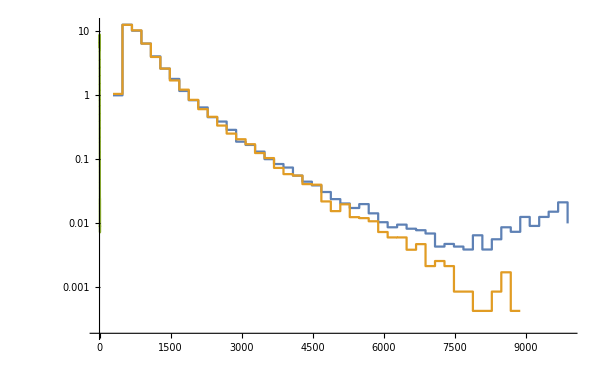

```mathematica
ListLogPlot[{MttOW,MttOWmllmin200,MttOWfromEVA},Joined->True,InterpolationOrder->0]
```